```mathematica
y[t_] := c(t^2 + 1)^(-2) + t^2 + 1
y'[t] + 4t/(t^2 + 1)* y[t] //Simplify
```

6 t

{1+t^2-4/((1+t^2)^2),1+t^2-2/((1+t^2)^2),1+t^2,1+t^2+2/((1+t^2)^2),1+t^2+4/((1+t^2)^2)}

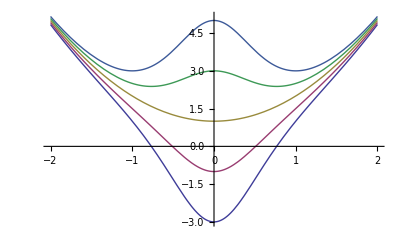

```mathematica
y[t] /.c -> { -4, -2, 0, 2, 4}
Plot[Evaluate [%], {t, -2, 2}]
```

```mathematica
Clear [c]
```

```mathematica
y[t_] := 10/(1+c*ⅇ^(-t/2))
y'[t] - y[t]/20(10 - y[t]) //Simplify
```

0

```mathematica
Solve[y[0] == 2, c]

y[t] = y[t] /.%
```

{{c→4}}

{{{{{{{{10/(1+4 ⅇ^(-t/2))}}}}}}}}

```mathematica
Plot [y[t], {t, -10, 15}]
```

-Graphics-